```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
fGen:=Module[{offDiag=RandomReal[{-1,1}]},{{1,offDiag},{offDiag, 1}}]
```

```mathematica
fGen1:=Module[{offDiag12=RandomReal[{-1,1}],offDiag13=RandomReal[{-1,1}],offDiag23=RandomReal[{-1,1}],aMatrix},aMatrix={{1,offDiag12,offDiag13},{offDiag12, 1,offDiag23},{offDiag13,offDiag23,1}};If[PositiveDefiniteMatrixQ@aMatrix,aMatrix,fGen1]]
```

```mathematica
aList=Table[fGen1,{i,1,1000000}];
```

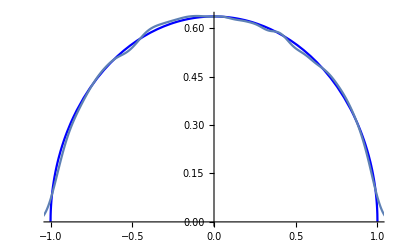

```mathematica
Show[Plot[PDF[TransformedDistribution[2 u -1,u\[Distributed]BetaDistribution[3/2,3/2]],x],{x,-1,1},PlotStyle->Blue] ,SmoothHistogram[aList[[All,1,2]]]]
```

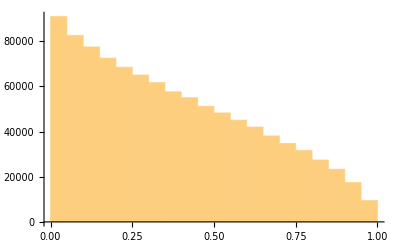

```mathematica
Histogram[Det/@aList]
```

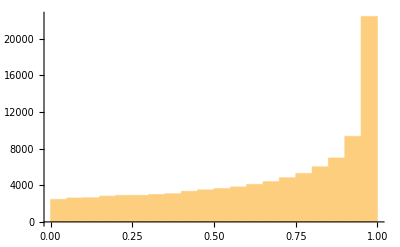

```mathematica
bList = Table[fGen,{i,1,100000}];
Histogram[Det/@bList]
```

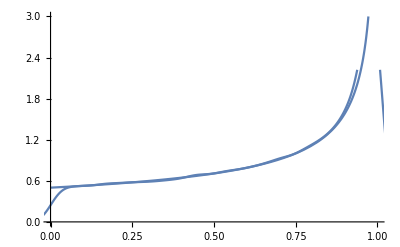

```mathematica
Show[Plot[PDF[BetaDistribution[1,1/2],x],{x,0,1},PlotRange->{Full,{0,3}}],SmoothHistogram[Det/@bList]]
```

```mathematica
Plot[PDF[TransformedDistribution[u v, {u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],x],{x,0,1},PerformanceGoal->"Speed"]
```

$Aborted

```mathematica
PDF[TransformedDistribution[u v, {u\[Distributed]BetaDistribution[1,1],v\[Distributed]BetaDistribution[3/2,1/2]}],0.5]
```

1.

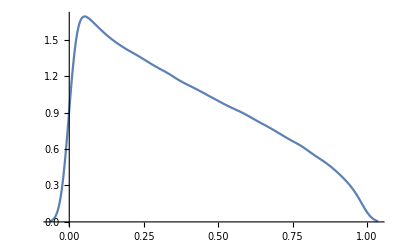

```mathematica
SmoothHistogram[RandomVariate[BetaDistribution[1,1],{1000000}]* RandomVariate[BetaDistribution[3/2,1/2],{1000000}]]
```